```mathematica
Clear[p]
```

```mathematica
bump[x_,p_,q_]=(1-Abs[x]^p)^q
```

(1-Abs[x]^p)^q

```mathematica
bumpx[x_,p_,q_]=D[bump[x,p,q],x]
```

-p q Abs[x]^(-1+p) (1-Abs[x]^p)^(-1+q) Abs'[x]

```mathematica
bumpxx[x_,p_,q_]=D[bumpx[x,p,q],x]
```

p^2 (-1+q) q Abs[x]^(-2+2 p) (1-Abs[x]^p)^(-2+q) Abs'[x]^2-(-1+p) p q Abs[x]^(-2+p) (1-Abs[x]^p)^(-1+q) Abs'[x]^2-p q Abs[x]^(-1+p) (1-Abs[x]^p)^(-1+q) Abs''[x]

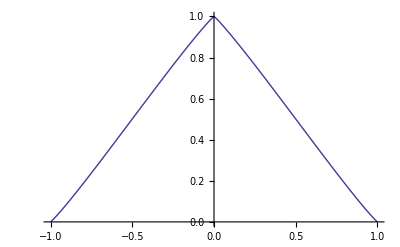

```mathematica
Plot[bump[x,1.1,1.1],{x,-1,1}]
```

```mathematica
Plot[bumpx[x,1.1,1.1],{x,-1,1}]
```

-Graphics-

```mathematica
Plot[bumpxx[x,1.1,1.1],{x,-1,1}]
```

-Graphics-

```mathematica
3Sqrt[3]
```

3 √3

```mathematica
N[3 √3]
```

5.19615